# Chapter 5 - Problem 6

Find the values of L ( < 4 nm), the separation between the rectangular barriers in a two - barrier structure, at which the transmission coefficient is equal one for an incoming electron with energy = 0.5 eV. Each barrier has a width of 2 nm and a height of 0.6 eV.

```mathematica
Clear["Global`*"]
(* Constants *)
e = 1.60217 * 10^-19; (* 1 electron volt(ev) = e Joules *)
h = 6.62607004 * 10^-34 ;(* planck's constant *)
m = 9.10938 * 10^-31; (* effective mass of an electron *)
ℏ = h/(2*Pi);
alpha = Sqrt[(2*m*e)/ℏ^2] * 10^-9;
```

```mathematica
PP[kx_,l_] = MatrixExp[-I*kx*l*PauliMatrix[3]];
PI[kL_, kR_] = MatrixExp[1/2* Log[kL/kR] * (PauliMatrix[1] - IdentityMatrix[2])];
```

```mathematica
en = 0.5;
V = 0.6;
bwidth = 2;
kwell= alpha * Sqrt[en - V];
kvacuum = alpha * Sqrt[en ];
```

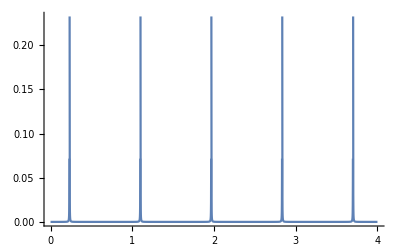

```mathematica
Mbarrier= PI[kvacuum,kwell].PP[kwell, bwidth].PI[kwell, kvacuum];
M = Mbarrier.PP[kvacuum,L].Mbarrier;
Plot[1/Abs[M[[1,1]]]^2,{L,0,4},PlotRange->All]
```

```mathematica
transmission = Abs[1/M[[1,1]]^2];
```

```mathematica
FindMaximum[transmission,{L,1}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.,{L→1.09981}}

```mathematica
FindMaximum[transmission,{L,0.1}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.,{L→0.232592}}

```mathematica
FindMaximum[transmission,{L,2}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.,{L→1.96702}}

```mathematica
FindMaximum[transmission,{L,2.9}]
```

FindMaximum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

{1.,{L→2.83424}}

```mathematica
FindMaximum[transmission,{L,3.7}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.,{L→3.70146}}